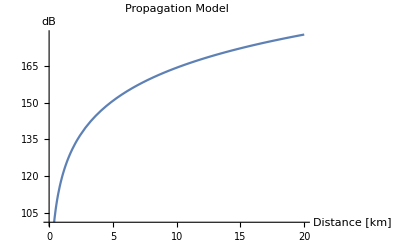

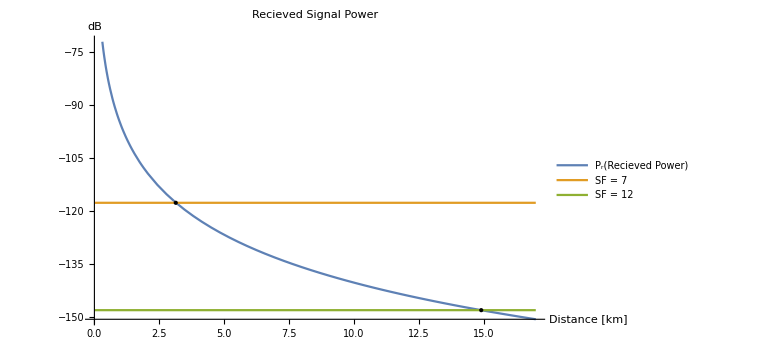

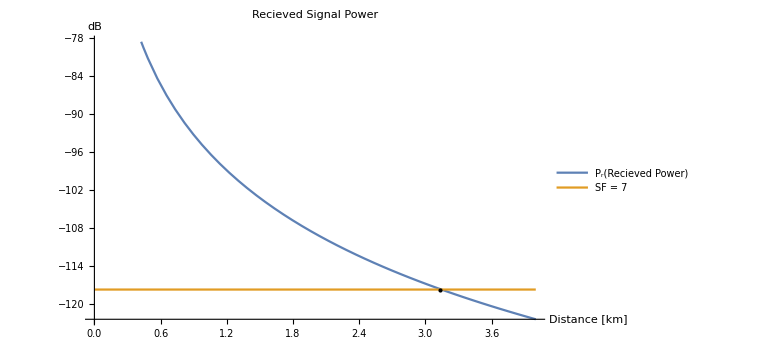

```mathematica
(*Hata model Open area*)
(*http://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.303.4057&rep=rep1&type=pdf*)
ClearAll["Global`*"]
Subscript[P, t]=20;
Subscript[G, t]=Subscript[G, r]=2;
Subscript[h, b]=Subscript[h, m]=1;
f =868.1;
x[h_]:=(1.1*Log10[f]-0.7)*h-(1.56*Log10[f]-0.8);
(*x[h_]:=3.2*(Log10[11.75*h])^2-4.97;*)
a=69.55+26.161*Log10[f]-13.82*Log10[Subscript[h, b]]-x[Subscript[h, m]];
b=44.9-6.55*Log10[Subscript[h, b]];
c=40.94+4.78*(Log10[f])^2-18.33*Log10[f];
Subscript[L, p][d_]:=a+b*Log10[d]-c;
Subscript[P, r][d_]:=Subscript[P, t]+Subscript[G, t]+Subscript[G, r]-Subscript[L, p][d];
intersection1={d,-117.67}/.NSolve[Subscript[P, r][d]==-117.6,d];
intersection2={d,-148}/.NSolve[Subscript[P, r][d]==-148,d];
Plot[Subscript[L, p][d],{d,0,20},AxesLabel->{"Distance [km]","dB"},PlotLabel->"Propagation Model"]
Plot[{Subscript[P, r][d],-117.67,-148},{d,0,17},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1],Point[intersection2]},PlotLabel-> "Recieved Signal Power",PlotLegends->{"P_r(Recieved Power)","SF = 7", "SF = 12"}]
Plot[{Subscript[P, r][d],-117.67},{d,0,4},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1]},PlotLabel-> "Recieved Signal Power",PlotLegends->{"P_r(Recieved Power)","SF = 7"}]
```

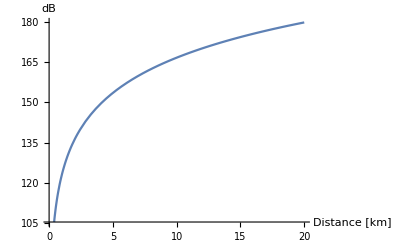

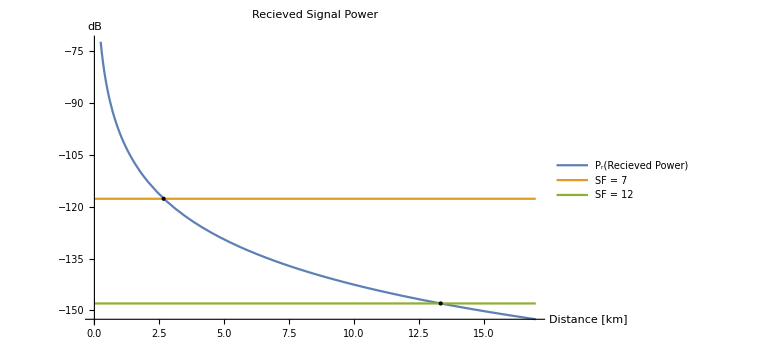

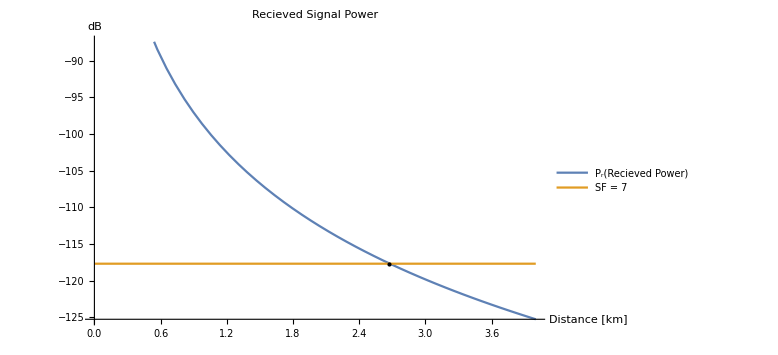

```mathematica
(*LEE propagation model*)
(*https://www.researchgate.net/publication/320819937_Analyses_and_optimization_of_Lee_propagation_model_for_LoRa_868_MHz_network_deployments_in_urban_areas*)
ClearAll["Global`*"]
x=43.5;
Subscript[L, 0]=89;
Subscript[F, 1][h_]:=(h/30.48)^2;
Subscript[F, 2][G_]:=G/4;
Subscript[F, 3][h_]:=(h/3);
Subscript[F, 4][f_,n_]:=(f/900)^-n;
Subscript[F, 5][G_]:=G/1;
Subscript[F, 0][hb_,Gb_,hm_,freq_,nn_,Gm_]:=Subscript[F, 1][hb]*Subscript[F, 2][Gb]*Subscript[F, 3][hm]*Subscript[F, 4][freq,nn]*Subscript[F, 5][Gm];
Subscript[L, 50][d_]:=Subscript[L, 0]+x*Log10[d]-10*Log10[Subscript[F, 0][1,2,1,868.1,2.5,2]];
Subscript[P, r][d_]:=Subscript[P, t]+Subscript[G, t]+Subscript[G, r]-Subscript[L, 50][d];
intersection1={d,-117.67}/.NSolve[Subscript[P, r][d]==-117.6,d];
intersection2={d,-148}/.NSolve[Subscript[P, r][d]==-148,d];
Plot[Subscript[L, 50][d],{d,0,20},AxesLabel->{"Distance [km]","dB"}]
Plot[{Subscript[P, r][d],-117.67,-148},{d,0,17},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1],Point[intersection2]},PlotLabel-> "Recieved Signal Power",PlotLegends->{"P_r(Recieved Power)","SF = 7", "SF = 12"}]
Plot[{Subscript[P, r][d],-117.67},{d,0,4},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1]},PlotLabel-> "Recieved Signal Power",PlotLegends->{"P_r(Recieved Power)","SF = 7"}]
(*
SF = 7 was calculated:
SF is between 6 and 12 and the estimated sensitivity is between -111 to -148 dBm
I took -148+111 to get the difference and divided it with difference from SF
This was then resulting in an increase of 6.66666 each spreading factor
therefore I added from the base value the increase of 6.6666 to get new spreading factor value. SF = 7 was then resulted in approx -117.67 dBm
*)
```